# KASUS TOV SCgrav Ho-Matsuo (juga pakai constant energy density)

## Pers gerak

```mathematica
pers100:=-1/(8 r[rs]^2)(2(α ν''[rs]-2 r[rs] ν'[rs] r'[rs])+4 r[rs] r''[rs]+2κ r[rs]^2 p0 Exp[ν[rs]/2]-α ν'[rs]^2)
pers200:=1/(4 r[rs]^2)(-α ν''[rs]-2(r[rs] r''[rs]+r'[rs]^2)+Exp[ν[rs]](2-κ r[rs]^2(2ρ0-p0 Exp[-ν[rs]/2])))
```

```mathematica
8 r[rs]^2(pers100-pers200)//Simplify
```

-4. ⅇ^ν[rs]+(-0.000377092 ⅇ^(ν[rs]/2)+72.304 ⅇ^ν[rs]) r[rs]^2+4. r'[rs]^2+4. r[rs] r'[rs] ν'[rs]+0.05 ν'[rs]^2-1.38778×10^-17 ν''[rs]

```mathematica
8 r[rs]^2(pers100+pers200)//Simplify
```

4. ⅇ^ν[rs]-72.304 ⅇ^ν[rs] r[rs]^2-4. r'[rs]^2+0.05 ν'[rs]^2+r[rs] (4. r'[rs] ν'[rs]-8. r''[rs])-0.2 ν''[rs]

```mathematica
ClearAll["Global`*"]
persν:=-4 ⅇ^ν[rs]+(-4 ⅇ^(ν[rs]/2) p0 κ+4 ⅇ^ν[rs] κ ρ0) r[rs]^2+4 r'[rs]^2+4 r[rs] r'[rs] ν'[rs]+α ν'[rs]^2
persr:=4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0 r[rs]^2-4 r'[rs]^2+α ν'[rs]^2+4 r[rs] (r'[rs] ν'[rs]-2 r''[rs])-4 α ν''[rs]
(*ρ0[rs_]=Piecewise[{{0./κ,rs>y},{25./κ,rs≤y}}]/.{y->-60.};*)

Solve[persν==0,ν'[rs]]//FullSimplify
limitαnol-> Solve[(persν/.{α->0})==0,ν'[rs]]//FullSimplify

Solve[persr==0,r''[rs]]//Simplify
```

{{ν'[rs]→-(2 (r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))))/α},{ν'[rs]→(2 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))))/α}}

limitαnol→{{ν'[rs]→(ⅇ^ν[rs]+(ⅇ^(ν[rs]/2) p0 κ-ⅇ^ν[rs] κ ρ0) r[rs]^2-r'[rs]^2)/(r[rs] r'[rs])}}

{{r''[rs]→(4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0 r[rs]^2-4 r'[rs]^2+4 r[rs] r'[rs] ν'[rs]+α ν'[rs]^2-4 α ν''[rs])/(8 r[rs])}}

```mathematica
rootpertama-> Series[-1/α 2 (r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))),{α,0,1}]//Simplify
rootkedua-> Series[1/α 2 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))),{α,0,1}]//Simplify
```

rootpertama→-(2 (r[rs] r'[rs]+√(r[rs]^2 r'[rs]^2)))/α+(-ⅇ^ν[rs]+(-ⅇ^(ν[rs]/2) p0 κ+ⅇ^ν[rs] κ ρ0) r[rs]^2+r'[rs]^2)/(√(r[rs]^2 r'[rs]^2))+(√(r[rs]^2 r'[rs]^2) (-ⅇ^ν[rs]+(-ⅇ^(ν[rs]/2) p0 κ+ⅇ^ν[rs] κ ρ0) r[rs]^2+r'[rs]^2)^2 α)/(4 r[rs]^4 r'[rs]^4)+O[α]^2

rootkedua→(2 (-r[rs] r'[rs]+√(r[rs]^2 r'[rs]^2)))/α+(ⅇ^ν[rs]+(ⅇ^(ν[rs]/2) p0 κ-ⅇ^ν[rs] κ ρ0) r[rs]^2-r'[rs]^2)/(√(r[rs]^2 r'[rs]^2))-((√(r[rs]^2 r'[rs]^2) (-ⅇ^ν[rs]+(-ⅇ^(ν[rs]/2) p0 κ+ⅇ^ν[rs] κ ρ0) r[rs]^2+r'[rs]^2)^2) α)/(4 (r[rs]^4 r'[rs]^4))+O[α]^2

rootkedua kembali ke TOV

### Jadi pers geraknya yg bisa ditulis eksplisit adalah

```mathematica
pers1:=ν'[rs]-> 1/α 2 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)))
(*Persamaan differensial metrik*)
pers2:=r''[rs]-> 1/(8 r[rs])(4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ r[rs]^2 ρ0-4 r'[rs]^2+4 r[rs] r'[rs] ν'[rs]+α ν'[rs]^2-4 α ν''[rs])(*Persamaan differensial radius*)
```

```mathematica
pers2/.{pers1,D[pers1,rs]}//Simplify
```

r''[rs]→1/(8 r[rs])(4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0 r[rs]^2-4 r'[rs]^2+(8 r[rs] r'[rs] (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2))))/α+(4 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)))^2)/α-8 (-r'[rs]^2-r[rs] r''[rs]+(4 r[rs] r'[rs] (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)+2 α (ⅇ^ν[rs] ν'[rs]-2 r'[rs] r''[rs])+r[rs]^2 ((ⅇ^(ν[rs]/2) p0 α κ-2 ⅇ^ν[rs] α κ ρ0) ν'[rs]+4 r'[rs] r''[rs]))/(4 √(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)))))

### Membandingkan dengan persaman TOV GR

```mathematica
ClearAll["Global`*"]
persν:=-4 ⅇ^ν[rs]+(-4 ⅇ^(ν[rs]/2) p0 κ+4 ⅇ^ν[rs] κ ρ0) r[rs]^2+4 r'[rs]^2+4 r[rs] r'[rs] ν'[rs]+0α ν'[rs]^2
persr:=4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0 r[rs]^2-4 r'[rs]^2+0α ν'[rs]^2+4 r[rs] (r'[rs] ν'[rs]-2 r''[rs])-4 0 α ν''[rs]
(*ρ0[rs_]=Piecewise[{{0./κ,rs>y},{25./κ,rs≤y}}]/.{y->-60.};*)

Solve[persν==0,ν'[rs]]//FullSimplify

Solve[persr==0,r''[rs]]//Simplify
```

{{ν'[rs]→(ⅇ^ν[rs]+(ⅇ^(ν[rs]/2) p0 κ-ⅇ^ν[rs] κ ρ0) r[rs]^2-r'[rs]^2)/(r[rs] r'[rs])}}

{{r''[rs]→(ⅇ^ν[rs]-ⅇ^ν[rs] κ ρ0 r[rs]^2-r'[rs]^2+r[rs] r'[rs] ν'[rs])/(2 r[rs])}}

### Backward calculation Ho-Matsuo

```mathematica
Clear["Global`*"]
pers1=-ν'[rs]+1/α 2 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)));
(*Persamaan differensial metrik*)
pers2=-r''[rs]+1/(8 r[rs])(4 ⅇ^ν[rs]-4 ⅇ^ν[rs] κ ρ0 r[rs]^2-4 r'[rs]^2+1/α 8 r[rs] r'[rs] (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)))+1/α 4 (-r[rs] r'[rs]+√(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)))^2-8 (-r'[rs]^2-r[rs] r''[rs]+(4 r[rs] r'[rs] (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)+2 α (ⅇ^ν[rs] ν'[rs]-2 r'[rs] r''[rs])+r[rs]^2 ((ⅇ^(ν[rs]/2) p0 α κ-2 ⅇ^ν[rs] α κ ρ0) ν'[rs]+4 r'[rs] r''[rs]))/(4 √(α (ⅇ^ν[rs]-r'[rs]^2)+r[rs]^2 (ⅇ^(ν[rs]/2) p0 α κ-ⅇ^ν[rs] α κ ρ0+r'[rs]^2)))));(*Persamaan differensial radius*)
```

```mathematica
{k->10./y}/.Solve[-60==y+10. Log[y/10.-1],y][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{k→0.99909}

```mathematica
GS=1.325*10^-12; MSS= 1.1155 * 10^15; 
α=0.05;
κ =8π GS;
a0:=10.
ρ00:=18.076
R:=10./0.9999999999728
rn=-20000000;
rs0=R+a0 Log[R/a0-1];
ν0=Log[1-a0/R];
ρ0=ρ00/κ;
p0=ρ00/κ Exp[ν0/2.];
s=NDSolve[{pers1==0,pers2==0,ν[rs0]==ν0,r[rs0]==R,r'[rs0]==(1-a0/R)},{ν,r},{rs,rs0,rn}]
```

{{ν→                              7
InterpolatingFunction[{{-2. 10 , -233.278}}, <>],r→                              7
InterpolatingFunction[{{-2. 10 , -233.278}}, <>]}}

0.00338286

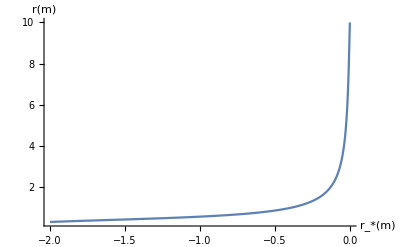

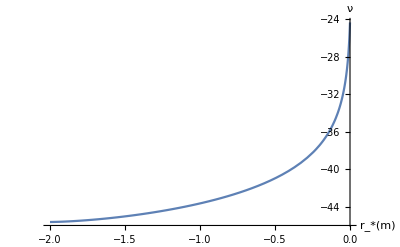

-Graphics-

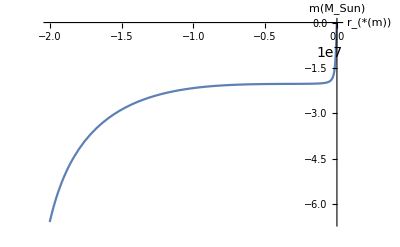

```mathematica
νo[rs_]=Evaluate[ν[rs]/.s][[1]];
ro[rs_]=Evaluate[r[rs]/.s][[1]];
Po[rs_]:=-ρ0 +p0 Exp[-νo[rs]/2]
mo[rs_]:=ro[rs]/(2GS MSS)(1-ro'[rs]^2 Exp[-νo[rs]])
 mo[rs0]
xx=rn;
Plot[ro[rs],{rs,xx,rs0},AxesLabel->{"r_*(m)","r(m)"},PlotRange->All]
Plot[νo[rs],{rs,xx,rs0},AxesLabel->{"r_*(m)","ν"},PlotRange->All]
Plot[Po[rs],{rs,xx,rs0},AxesLabel->{"r_*(m)","P (MeV fm^-3)"},PlotRange->All]
Plot[mo[rs],{rs,xx,rs0},AxesLabel->{"r_(*(m))","m(M_Sun)"},PlotRange->All]
```

```mathematica
ro[rn]
```

0.316342

```mathematica
Sqrt[0.05]
```

0.223607

```mathematica
ClearAll[x]
x[i_]:=rn+i(rs0-rn)/1000
data:=Table[{x[i]/100000,Po[x[i]]*10^-15,mo[x[i]], νo[x[i]], ro[x[i]]},{i,0,1000}]
Export[FileNameJoin[{NotebookDirectory[],"TOV-reverse-5.0.1a.dat"}],data]
```

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\TOV-reverse-5.0.1a.dat

### Forward Ho-Matsuo

{{ν→                              7
InterpolatingFunction[{{-2. 10 , -233.278}}, <>],r→                              7
InterpolatingFunction[{{-2. 10 , -233.278}}, <>]}}

0.00338286

-Graphics-

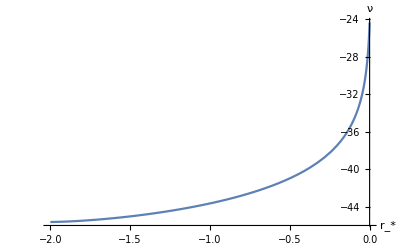

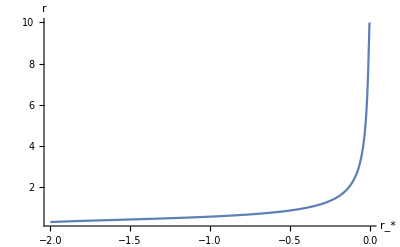

```mathematica
s1=NDSolve[{pers1==0,pers2==0,ν[rn]==νo[rn],r[rn]==ro[rn],r'[rn]==ro'[rn]},{ν,r},{rs,rn,rs0}]
νo1[rs_]=Evaluate[ν[rs]/.s1][[1]];
ro1[rs_]=Evaluate[r[rs]/.s1][[1]];
Po1[rs_]:=-ρ0 +p0 Exp[-νo1[rs]/2]
mo1[rs_]:=ro[rs]/(2GS MSS)(1-ro'[rs]^2 Exp[-νo[rs]])
 mo1[rs0]

xx=rn;
Plot[Po1[rs],{rs,xx,rs0},AxesLabel->{"r_*","P"},PlotRange->All]
Plot[νo1[rs],{rs,xx,rs0},AxesLabel->{"r_*","ν"},PlotRange->All]
Plot[ro1[rs],{rs,xx,rs0},AxesLabel->{"r_*","r"},PlotRange->All]
```

### Perbandingan Backward vs Forward

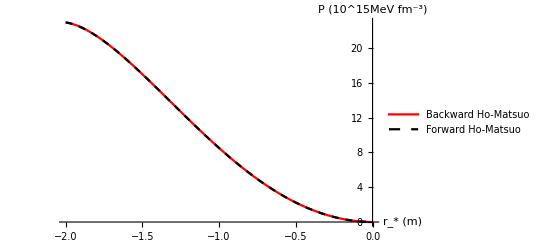

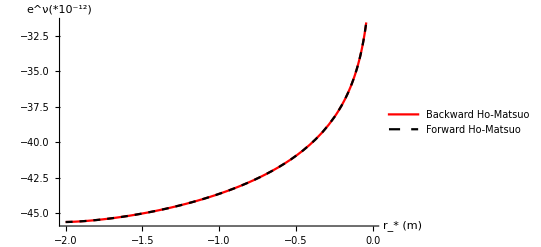

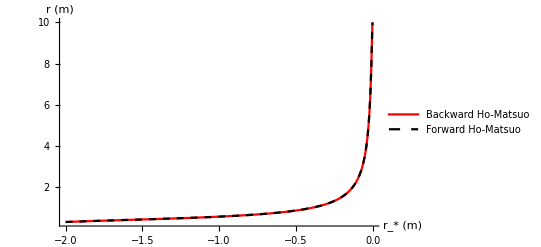

```mathematica
Plot[{Po[rs]*10^-15, Po1[rs]*10^-15},{rs,rn,rs0},PlotRange->All,AxesLabel->{"r_* (m)","P (10^15MeV fm^-3)"},PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Backward Ho-Matsuo","Forward Ho-Matsuo"}]
Plot[{νo[rs],νo1[rs]},{rs,rn,rs0},PlotRange->Automatic,AxesLabel->{"r_* (m)","e^ν(*10^-12)"},PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Backward Ho-Matsuo","Forward Ho-Matsuo"}]
Plot[{ro[rs],ro1[rs]},{rs,rn,rs0},PlotRange->All,AxesLabel->{"r_* (m)","r (m)"},PlotStyle->{{Red,Thick},{Black,Dashed}},PlotLegends->{"Backward Ho-Matsuo","Forward Ho-Matsuo"}]
```

### Forward TOV GR

```mathematica
pers3:=ν'[rs]- (ⅇ^ν[rs]+(ⅇ^(ν[rs]/2) p0 κ-ⅇ^ν[rs] κ ρ0) r[rs]^2-r'[rs]^2)/(r[rs] r'[rs])
(*Persamaan differensial metrik*)
pers4:=r''[rs]-(ⅇ^ν[rs]-ⅇ^ν[rs] κ ρ0 r[rs]^2-r'[rs]^2+r[rs] r'[rs] ν'[rs])/(2 r[rs])
(*Persamaan differensial radius*)
```

```mathematica
rs0
```

-233.278

```mathematica
?WhenEvent
```

WhenEvent[event,action] specifies an action that occurs when the event triggers it for equations in NDSolve and related functions.

NDSolve::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between rs = 1.87017×10^6 and rs = 1.87182×10^6.

{{ν→                              7            6
InterpolatingFunction[{{-2. 10 , 1.87171 10 }}, <>],r→                              7            6
InterpolatingFunction[{{-2. 10 , 1.87171 10 }}, <>]}}

1.87171×10^6

-0.000976563

0.999943

-Graphics-

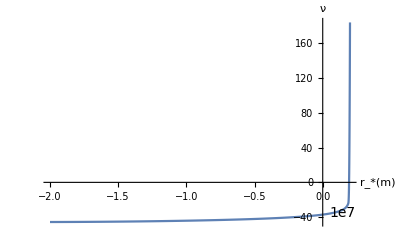

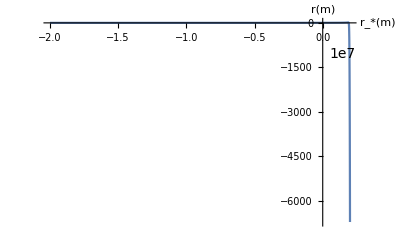

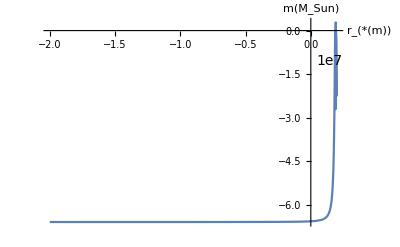

```mathematica
rs00=2000000.;
s3=NDSolve[{pers3==0,pers4==0,ν[rn]==νo[rn],r[rn]==ro[rn],r'[rn]==ro'[rn]},{ν,r},{rs,rn,rs00},Method->{"EventLocator","Event" :>{-ρ0 +p0 Exp[-ν[rs]/2]},"EventAction":>Throw[rsStar=rs,"StopIntegration"]}]
(*R=a0/0.9999999999728
ν0=Log[1-a0/R];
ρ0=ρ00/κ;
p0=ρ00/κ Exp[ν0/2.];
s3=NDSolve[{pers3==0,pers4==0,ν[rs0]==ν0,r[rs0]==R,r'[rs0]==(1-a0/R)},{ν,r},{rs,rs0,rn}]*)
rsStar
νotov[rs_]=Evaluate[ν[rs]/.s3][[1]];
rotov[rs_]=Evaluate[r[rs]/.s3][[1]];
Potov[rs_]:=-ρ0 +p0 Exp[-νotov[rs]/2]
motov[rs_]:=rotov[rs]/(2GS MSS)(1-rotov'[rs]^2 Exp[-νotov[rs]])
Potov[rsStar]
2GS MSS motov[rsStar]/rotov[rsStar]

xx=rn;
Plot[Potov[rs],{rs,xx,rs00},AxesLabel->{"r_*(m)","P (MeV fm^-3)"},PlotRange->All]
Plot[νotov[rs],{rs,xx,rs00},AxesLabel->{"r_*(m)","ν"},PlotRange->All]
Plot[rotov[rs],{rs,xx,rs00},AxesLabel->{"r_*(m)","r(m)"},PlotRange->All]
Plot[motov[rs],{rs,xx,rs00},AxesLabel->{"r_(*(m))","m(M_Sun)"},PlotRange->All]
```

### Perbandingan Backward vs Forward

Keluarin datanya

```mathematica
R-a0
```

2.71999×10^-10

```mathematica
ClearAll[x]
x[i_]:=rn+i(rsStar-rn)/1000
data:=Table[{x[i]/100000, Potov[x[i]]*10^-15, motov[x[i]], νotov[x[i]], rotov[x[i]]},{i,0,1000}]
Export[FileNameJoin[{NotebookDirectory[],"TOV-reverse-5.0.1.dat"}],data]
```

C:\Users\ilham\Dropbox\00 SCGrav\ceknumerik\TOV-reverse-5.0.1.dat

```mathematica
compactness-> {2GS MSS mo1[rs0]/ro1[rs0],2GS MSS motov[rsStar]/rotov[rsStar]}
pc-> {Po1[rn],Potov[rn]}
```

compactness→{0.999986,0.999943}

pc→{2.29322×10^16,2.29322×10^16}

```mathematica
Subscript[r, starS]->Solve[-60==y+10. Log[y/10.-1],y]
Subscript[r, star]->Solve[-56.685==y+10. Log[y/10.-1],y]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

r_starS→{{y→10.0091}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

r_star→{{y→10.0127}}

```mathematica
10.0091+10. Log[10.0091/10.-1]
```

-60.0116